ADDITIVE LOGISTIC PROCESSES. SOME CODE

Author: Lorenzo Torricelli.  lorenzo.torricelli@unipr.it
Code can be freely used and modified, but its for illustration purposes only and it comes with no guarantee on the accuracy of results 

Reference: P. Carr and L. Torricelli "Additive logisitc processes in option pricing" 2021. Retrivable at SSRN https://papers.ssrn.com/sol3/papers.cfm?abstract_id=3647466

This notebook implements some formulae in the paper Carr and Torricelli 2021 and produces visual outputs. 
CPDA : conjugate - power Dagum additive model. Positive martingale pricing model of additive type (Markov with inhomeogeneous dependent increments) price whose log-returns are leptokurtic and skewed (skew-logistic distribution). 
SSLA : self - similar logistic additive model. Real-valued symmetric martingale pricing  model of additive type with centered returns and leptokurtosis.

The models produce closed formula for vanilla prices, PDFs, CDFs, tractable expressions for exotic derviatives, flexible volatility smile/skew and term sturcture, with a parsimonious parametrization.  Both models are pure jump.

Term functions for the CPDA and SSLA models.  Section 5 Carr and Torricelli.
  t : time to maturity
sigma : "volatility"
H : "self-similarity" parameter

```mathematica
b[t_, sigma_,  H_]:=(1-Exp[- t sigma ^(1/H)])^(H)
```

```mathematica
s[t_, sigma_, H_]:=sigma t^H
```

Option Prices.  Section 2 Carr and Torricelli
t : time to maturity
K : strike price
S : spot price

```mathematica
CPDAPut[K_, S_, t_, sigma_,H_]:=(K^(1/b[t, sigma,  H])+S^(1/b[t, sigma,  H] ))^b[t, sigma,  H]-S
SSLAPut[K_, S_, t_, sigma_,H_]:=s[t, sigma, H] Log[1+Exp[-(S-K)/ s[t, sigma, H] ]]
CPDACall[K_, S_, t_, sigma_,H_]:=(K^(1/b[t, sigma,  H])+S^(1/b[t, sigma,  H] ))^b[t, sigma,  H]-K
SSLACall[K_, S_, t_, sigma_,H_]:=s[t, sigma, H] Log[1+Exp[(S-K)/ s[t, sigma, H] ]]
```

Logistic and Skew Logistic probability density functions. Section 3 Carr and Torricelli
x : density variable
mu : location parameter
alpha : skew parameter
sigma : scale parameter

```mathematica
SkewLogisticPDF[x_, mu_, alpha_, sigma_]:=alpha/sigma Exp[(x-mu)alpha/sigma]/(1+Exp[(x-mu)/sigma])^(1+alpha)
LogisticPDF[x_, mu_,  sigma_]:=SkewLogisticPDF[x, mu, 1, sigma]
CPDALogReturns[x_,t_,sigma_,H_]:=SkewLogisticPDF[x, 0, 1-b[t, sigma,  H] ,b[t, sigma,  H] ]
SSLAReturns[x_,t_,sigma_,H_]:=LogisticPDF[x, 0,s[t, sigma,  H]]
```

Forumlae for the expected value and higher - order cumulants of the CPDA and SSLA models . Section 5 Carr and Torricelli.
 n : cumulant order. Must be even for the SSLA model

```mathematica
CPDAMean[ t_, sigma_,H_]:=PolyGamma[0, 1-b[t,sigma,H]]+EulerGamma
CPDACumulants[n_, t_, sigma_,H_]:=b[t, sigma, H]^n(Zeta[n]Factorial[n-1]+ PolyGamma[n-1, 1-b[t,sigma,H]]) 
SSLACumulants[n_,t_, sigma_, H_]:=2 s[t, sigma, H]^n Zeta[n]Factorial[n-1]
CPDAVariance[ t_, sigma_,H_]:=CPDACumulants[2, t, sigma,H]
CPDASkewness[t_, sigma_,H_]:=CPDACumulants[3, t, sigma,H]/CPDAVariance[ t, sigma,H]^1.5
CPDAKurtosis[t_, sigma_,H_]:=CPDACumulants[4, t, sigma,H]/CPDAVariance[ t ,sigma,H]^2
SSLAVariance[ t_, sigma_,H_]:=SSLACumulants[2, t, sigma,H]
SSLAKurtosis[ t_, sigma_,H_]:=SSLACumulants[4, t, sigma,H]/SSLAVariance[ t, sigma,H]^2
```

Density Plots
Log returns of the CPDA model versus Black-Scholes. Shape change in CPDA, only location scale in BS. Use H=0.5 to get the normal matching for small times.
 Returns of the SSLA versus Normal (Bachelier) with variances matched. Leptokurtosis slight but visible (equals 6/5).

```mathematica
Module[{xmin, xmax, sigmaMin, sigmaMax, Hmin, Hmax, Tmin, Tmax},
xmin=-2;
xmax=2;
Hmin=0.2;
Hmax=1;
sigmaMin=0.1;
sigmaMax=1;
Tmin=0.5;
 Tmax=6;
Manipulate[Plot[  { SSLAReturns[x,t,sigma,H] ,PDF[NormalDistribution[  0,  t^(H)sigma  Pi/Sqrt[3]], x]},{x, xmin,xmax},PlotStyle->{Thick, Thick},PlotRange->{0, 2.5}, PlotLabel-> "SSLA Log-returns vs Normal", PlotStyle->{Thick, Thick}], {t, Tmin, Tmax},{sigma,sigmaMin, sigmaMax}, {H,Hmin, Hmax}]

Manipulate[Plot[  { CPDALogReturns[x,t,sigma,H] ,PDF[NormalDistribution[  -sigma^2t/2, sigma Sqrt[ t]], x]},{x, xmin,xmax},  PlotStyle->{Thick, Thick},PlotLabel->"CPDA Log-returns vs Normal", PlotRange->{0, 3}, PlotStyle->{Thick, Thick}], {t, Tmin, Tmax},{sigma,sigmaMin, sigmaMax},{H,Hmin, Hmax} ]
]
```

Cumulants plots
Superlinear growth of the normalized cumulants, better captures market implied moments. Homgeneous models, skewness and kurtosis fall to zero. CPDA: various shapes, eventually asymptoting, but not decreasing to zero. Steep slope of the skewness in zero. SSLA constant Kurtosis (logistic distribution property- kurtosis independent of scale).

```mathematica
Module[{Tmax,Hmax, sigmaMax, Tmin,Hmin, sigmaMin},
Tmax=3;
Tmin=0;
Hmax=1;
Hmin=0.3;
sigmaMin=0.1;
sigmaMax=1;

Manipulate[Plot[{CPDAVariance[ t, sigma,H],  t },{t, Tmin,Tmax}, AxesLabel->{t }, PlotLabel->"CPDA Log-returns variance vs time homeogeneous model", PlotStyle->{{Blue,Thick}, {Purple,Thick}}, PlotRange->{0,3}],  {sigma, sigmaMin, sigmaMax}, {H, Hmin, Hmax}]
Manipulate[Plot[{CPDASkewness[ t, sigma,H], -1/Sqrt[t]},{t, Tmin,Tmax}, AxesLabel->{ t }, PlotLabel->"CPDA Log-returns skewness vs time homeogeneous model", PlotRange->{-2,0}, PlotStyle->{{Blue,Thick}, {Purple,Thick}}], {sigma, sigmaMin, sigmaMax},{H, Hmin, Hmax}]
Manipulate[Plot[{CPDAKurtosis[ t, sigma,H], 1/t},{t, Tmin,Tmax}, AxesLabel->{ t }, PlotLabel->"CPDA Log-retruns kurtosis vs time homeogeneous model", PlotStyle->{{Blue,Thick}, {Purple,Thick}}, PlotRange->{0,3}], {sigma, sigmaMin, sigmaMax},{H, Hmin, Hmax}]

]
```

```mathematica
Module[{Tmax,Hmax, sigmaMax, Tmin,Hmin, sigmaMin},
Tmax=3;
Tmin=0;
Hmax=1;
Hmin=0.3;
sigmaMin=0.1;
sigmaMax=1;

Manipulate[Plot[{SSLAVariance[ t, sigma,H],  t },{t, Tmin,Tmax}, AxesLabel->{t }, PlotLabel->"SSLA returns variance vs Black Scholes", PlotStyle->{{Blue,Thick}, {Purple,Thick}}], {sigma, sigmaMin, sigmaMax}, {H, Hmin, Hmax}]
Manipulate[Plot[{SSLAKurtosis[ t, sigma,H], 1/ t},{t, Tmin,Tmax}, AxesLabel->{ t }, PlotLabel->"SSLA returns kurtosis vs Black Scholes", PlotStyle->{{Blue,Thick}, {Purple,Thick}},  PlotRange->{0,3}], {sigma, sigmaMin, sigmaMax},{H, Hmin, Hmax}]
]
```

Implied volatility surfaces

Implied volatilities finders (normal and lognormal)

```mathematica
normCdf[x_]:=1/2*(1+Erf[x/Sqrt[2]]);
normPdf[x_]:= Exp[-x^2/2]/Sqrt[2 Pi];
d1[s_, sigma_, k_,t_, r_]:=(r*t +  Log[s/k])/(sigma*Sqrt[t])+ (sigma*Sqrt[t])/2;
d2[s_,sigma_,k_,t_,r_]:=d1[s,sigma, k,t,r]-sigma*Sqrt[t];

BlackScholesCall[s_,k_,sigma_,t_,r_]:=s normCdf[d1[s,sigma,k,t,r]]-k Exp[-r t]normCdf[d2[s,sigma,k,t,r]]
BachelierCall[s_,  k_, sigma_, t_, r_]:= (s- Exp[-r t] k)*normCdf[( s-Exp[-r t]k)/( sigma Sqrt[ t])]+ sigma Sqrt[t]normPdf[( s-k Exp[-r t])/( sigma Sqrt[ t])]

ImpliedVolLogNormal[s_,k_,t_,r_,price_]:=  sigma/. FindRoot[BlackScholesCall[s,k,sigma,t, r]==price,{sigma, 0.2}];

ImpliedVolNormal[s_,k_,t_,r_,price_]:=  sigma/. FindRoot[BachelierCall[s, k, sigma,t, r]==price,{sigma, 0.2}];
```

Volatility surfaces for the SSLA and  CPDA model as functions of the model inputs

```mathematica
CPDAVolSurface[S0_,
sigma_,H_]:=Module[{Tmin, Tmax,  Kmax, Kmin, Nstrikes, Ntimes, Tstep, Kstep},
Kmin=S0 0.6;
Kmax=S0 1.4;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Ntimes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Nstrikes}]];


CPDAPrices=CPDACall[Ktab, S0, Ttab, sigma,H];


Table[ImpliedVolLogNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  CPDAPrices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]

SSLANormalVolSurface[S0_,
sigma_,H_]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.6;
Kmax=S0 1.4;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Ntimes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Nstrikes}]];


SSLAPrices=SSLACall[Ktab, S0, Ttab, sigma,H];
Table[ImpliedVolNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  SSLAPrices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]

SSLALogNormalVolSurface[S0_,
sigma_,H_]:=Module[{ Tmin, Tmax, Kstep, Kmax, Kmin, Nstrikes, Ntimes, Tstep },
Kmin=S0 0.6;
Kmax=S0 1.4;
Ntimes=15;
Nstrikes=15;
Kstep=(Kmax-Kmin)/(Nstrikes-1);
Tmin=0.5;
Tmax=2;
Tstep=(Tmax-Tmin)/(Ntimes-1);
Ktab=Table[Range[Kmin, Kmax, Kstep],{Ntimes}];
Ttab=Transpose[Table[Range[Tmin, Tmax, Tstep],{Nstrikes}]];


SSLAPrices=SSLACall[Ktab, S0, Ttab, sigma,H];
Table[ImpliedVolLogNormal[S0,Ktab[[i,j]],Ttab[[i,j]], 0,  SSLAPrices[[i,j]] ], {j,Nstrikes}, {i,Ntimes}] 
]
```

Speed Test

```mathematica
Timing[CPDAVolSurface[1, 0.5,0.25]]
Timing[SSLANormalVolSurface[1, 0.5,0.25]]
Timing[SSLALogNormalVolSurface[1, 0.5,0.25]]
```

{0.188,{{1.25481,1.20585,1.1671,1.13533,1.10861,1.08567,1.06569,1.04804,1.03231,1.01814,1.0053,0.993581,0.982825,0.972903,0.96371},{1.2476,1.19955,1.16147,1.13022,1.10391,1.08132,1.06162,1.04422,1.0287,1.01472,1.00204,0.990468,0.979842,0.970037,0.960952},{1.24209,1.19474,1.15718,1.12634,1.10035,1.07802,1.05854,1.04133,1.02597,1.01213,0.999578,0.988115,0.977588,0.967874,0.95887},{1.23801,1.19119,1.15401,1.12347,1.09772,1.07559,1.05627,1.0392,1.02396,1.01023,0.997767,0.986386,0.975933,0.966284,0.95734},{1.23512,1.18867,1.15178,1.12145,1.09587,1.07388,1.05468,1.0377,1.02255,1.00889,0.996493,0.98517,0.974769,0.965168,0.956266},{1.23324,1.18704,1.15033,1.12013,1.09466,1.07276,1.05364,1.03673,1.02163,1.00802,0.995667,0.984382,0.974014,0.964444,0.95557},{1.2322,1.18614,1.14953,1.11941,1.094,1.07215,1.05307,1.0362,1.02113,1.00754,0.995214,0.98395,0.973601,0.964047,0.955189},{1.23189,1.18587,1.14928,1.11919,1.0938,1.07196,1.05289,1.03603,1.02097,1.0074,0.995075,0.983817,0.973474,0.963925,0.955071},{1.23217,1.18611,1.1495,1.11939,1.09398,1.07213,1.05305,1.03618,1.02111,1.00753,0.995199,0.983935,0.973587,0.964034,0.955176},{1.23296,1.1868,1.15011,1.11994,1.09449,1.0726,1.05349,1.03659,1.02149,1.00789,0.995545,0.984266,0.973904,0.964338,0.955468},{1.23418,1.18786,1.15105,1.12079,1.09526,1.07332,1.05416,1.03722,1.02209,1.00845,0.99608,0.984776,0.974392,0.964806,0.955918},{1.23575,1.18923,1.15227,1.12189,1.09627,1.07425,1.05503,1.03803,1.02286,1.00918,0.996773,0.985437,0.975025,0.965413,0.956502},{1.23763,1.19086,1.15372,1.1232,1.09748,1.07537,1.05606,1.03901,1.02377,1.01005,0.9976,0.986227,0.975781,0.966139,0.9572},{1.23976,1.19271,1.15537,1.1247,1.09884,1.07663,1.05724,1.04011,1.02482,1.01104,0.998541,0.987125,0.976641,0.966964,0.957994},{1.24209,1.19474,1.15718,1.12634,1.10035,1.07802,1.05854,1.04133,1.02597,1.01213,0.999578,0.988115,0.977588,0.967874,0.95887}}}

{0.094,{{1.04645,0.99572,0.955229,0.921776,0.89343,0.868941,0.847459,0.82838,0.81126,0.795765,0.781637,0.768674,0.756714,0.745626,0.735301},{1.04298,0.992712,0.952557,0.919363,0.891223,0.866904,0.845564,0.826605,0.809589,0.794185,0.780137,0.767245,0.755349,0.744318,0.734045},{1.04001,0.990133,0.950268,0.917297,0.889336,0.865163,0.843944,0.825089,0.808162,0.792836,0.778857,0.766026,0.754184,0.743202,0.732974},{1.03755,0.988,0.948376,0.915591,0.887778,0.863726,0.842609,0.823839,0.806987,0.791725,0.777802,0.765022,0.753225,0.742284,0.732092},{1.03561,0.986325,0.946892,0.914254,0.886557,0.8626,0.841563,0.822861,0.806066,0.790855,0.776977,0.764236,0.752475,0.741566,0.731403},{1.03422,0.985121,0.945826,0.913293,0.88568,0.861792,0.840812,0.822159,0.805406,0.790231,0.776386,0.763673,0.751937,0.741051,0.730909},{1.03338,0.984396,0.945183,0.912714,0.885152,0.861306,0.84036,0.821736,0.805009,0.789856,0.77603,0.763334,0.751614,0.740741,0.730612},{1.0331,0.984153,0.944969,0.912521,0.884976,0.861143,0.840209,0.821595,0.804876,0.789731,0.775911,0.763221,0.751506,0.740638,0.730513},{1.03338,0.984396,0.945183,0.912714,0.885152,0.861306,0.84036,0.821736,0.805009,0.789856,0.77603,0.763334,0.751614,0.740741,0.730612},{1.03422,0.985121,0.945826,0.913293,0.88568,0.861792,0.840812,0.822159,0.805406,0.790231,0.776386,0.763673,0.751937,0.741051,0.730909},{1.03561,0.986325,0.946892,0.914254,0.886557,0.8626,0.841563,0.822861,0.806066,0.790855,0.776977,0.764236,0.752475,0.741566,0.731403},{1.03755,0.988,0.948376,0.915591,0.887778,0.863726,0.842609,0.823839,0.806987,0.791725,0.777802,0.765022,0.753225,0.742284,0.732092},{1.04001,0.990133,0.950268,0.917297,0.889336,0.865163,0.843944,0.825089,0.808162,0.792836,0.778857,0.766026,0.754184,0.743202,0.732974},{1.04298,0.992712,0.952557,0.919363,0.891223,0.866904,0.845564,0.826605,0.809589,0.794185,0.780137,0.767245,0.755349,0.744318,0.734045},{1.04645,0.99572,0.955229,0.921776,0.89343,0.868941,0.847459,0.82838,0.81126,0.795765,0.781637,0.768674,0.756714,0.745626,0.735301}}}

{0.187,{{1.39028,1.32848,1.27946,1.2392,1.20529,1.17615,1.15074,1.1283,1.10828,1.09026,1.07392,1.05901,1.04533,1.03272,1.02104},{1.32394,1.26497,1.21813,1.1796,1.14711,1.11917,1.09477,1.0732,1.05393,1.03657,1.02082,1.00643,0.993213,0.981016,0.969712},{1.26574,1.20928,1.16437,1.1274,1.09618,1.06932,1.04584,1.02506,1.00649,0.989738,0.974525,0.960618,0.947836,0.93603,0.925078},{1.21426,1.16002,1.11684,1.08126,1.05119,1.02529,1.00264,0.982581,0.964638,0.948448,0.933732,0.920272,0.907892,0.896451,0.885831},{1.16843,1.11616,1.07451,1.04017,1.01113,0.9861,0.964195,0.944789,0.927419,0.911737,0.897476,0.884426,0.872416,0.861312,0.850999},{1.1274,1.07688,1.03659,1.00335,0.975235,0.950986,0.929756,0.910937,0.894086,0.878866,0.86502,0.852343,0.840673,0.829878,0.81985},{1.09051,1.04153,1.00245,0.9702,0.942903,0.919354,0.898728,0.880439,0.864057,0.849257,0.835787,0.823451,0.812091,0.80158,0.791812},{1.05721,1.00959,0.971589,0.94021,0.913646,0.890723,0.870641,0.852829,0.83687,0.822448,0.80932,0.797294,0.786217,0.775964,0.766435},{1.02707,0.98064,0.943582,0.91298,0.887068,0.864705,0.84511,0.827727,0.812149,0.79807,0.785251,0.773506,0.762685,0.752669,0.743356},{0.9997,0.954317,0.918091,0.888175,0.862844,0.84098,0.821819,0.804821,0.789586,0.775815,0.763275,0.751785,0.741198,0.731396,0.722282},{0.974798,0.930322,0.894827,0.865516,0.840699,0.819278,0.800506,0.783852,0.768925,0.755432,0.743144,0.731883,0.721508,0.7119,0.702966},{0.95209,0.908401,0.873543,0.844765,0.8204,0.799373,0.780948,0.764601,0.74995,0.736706,0.724645,0.713592,0.703408,0.693977,0.685207},{0.931344,0.888332,0.854029,0.825716,0.801752,0.781073,0.762954,0.746882,0.732478,0.719457,0.7076,0.696735,0.686723,0.677452,0.66883},{0.912356,0.869925,0.836101,0.808195,0.784582,0.76421,0.746364,0.730535,0.716351,0.703531,0.691857,0.68116,0.671303,0.662177,0.653689},{0.894947,0.853011,0.819601,0.792048,0.768741,0.74864,0.731035,0.715423,0.701435,0.688793,0.677284,0.666738,0.657021,0.648025,0.639659}}}

The following tests produces volatility surfaces for the SSLA and  CPDA model. Dynamical response to sigma and H anlysed.

```mathematica
Module[{S0},
S0=1;
Manipulate[ListPlot3D[CPDAVolSurface[S0, sigma,H] , DataRange->{{S0 0.6, S0 1.4}, {0.5, 2} }, PlotLabel->"CPDA Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1}]
Manipulate[ListPlot3D[SSLANormalVolSurface[S0, sigma,H] , DataRange->{{S0 0.6, S0 1.4}, {0.5, 2} }, PlotLabel->"SSLA Normal Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1}]
Manipulate[ListPlot3D[SSLALogNormalVolSurface[S0, sigma,H] , DataRange->{{S0 0.6, S0 1.4}, {0.5, 2} }, PlotLabel->"SSLA LogNormal Volatility Surface"], {sigma, 0.1, 1}, {H, 0.1, 1}]

]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function.  You may need more than MachinePrecision digits of working precision to meet these tolerances.

Plots on the Paper "Additive Logistic Processes in Option pricing"

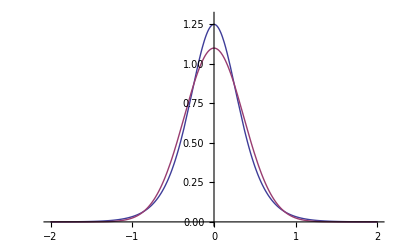

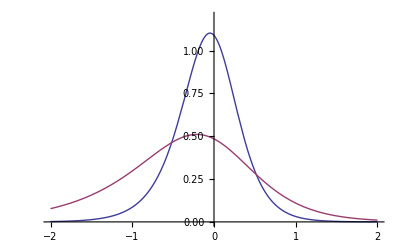

```mathematica
Plot[  { SSLAReturns[x,1,0.2,0.5] ,PDF[NormalDistribution[  0, 0.2  Pi/Sqrt[3]], x]},{x, -2,2},PlotStyle->{Thick, Thick},PlotRange->{0, 1.3}, PlotStyle->{Thick, Thick}]
Plot[  { CPDALogReturns[x,0.5, .3,0.5] ,CPDALogReturns[x, 2, .3,0.5]},{x, -2,2},  PlotStyle->{Thick, Thick}, PlotRange->{0, 1.2}, PlotStyle->{Thick, Thick}]
```

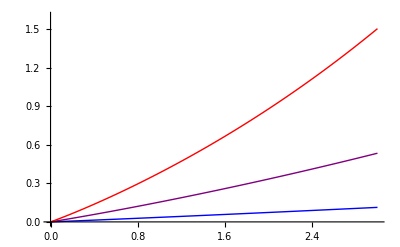

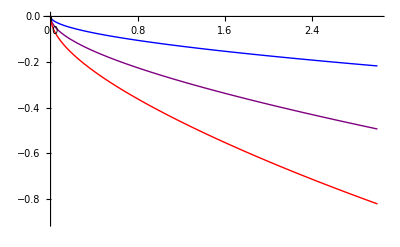

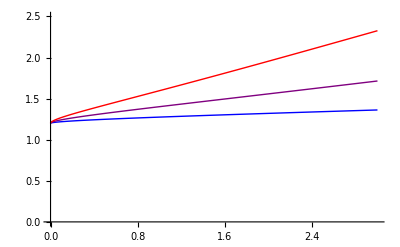

```mathematica
Plot[{CPDAVariance[ t,  0.1, 0.5], CPDAVariance[ t,  0.2, 0.5], CPDAVariance[ t,  0.3, 0.5]   },{t, 0,3}, AxesLabel->{t }, PlotStyle->{{Blue,Thick}, {Purple,Thick},  {Red,Thick}}, PlotRange->{0,1.6}]
Plot[{CPDASkewness[ t,  0.1, 0.5], CPDASkewness[ t,  0.2, 0.5], CPDASkewness[ t,  0.3, 0.5]},{t, 0,3}, AxesLabel->{ t },  PlotRange->{-.9,0}, PlotStyle->{{Blue,Thick}, {Purple,Thick}, {Red,Thick}}]
Plot[{CPDAKurtosis[ t,  0.1, 0.5], CPDAKurtosis[ t,  0.2, 0.5], CPDAKurtosis[ t,  0.3, 0.5]},{t, 0,3}, AxesLabel->{ t }, PlotStyle->{{Blue,Thick}, {Purple,Thick}, {Red,Thick}}, PlotRange->{0,2.5}]
```